```mathematica
Remove[BB, CC]
aa := 1
dd := 1
```

```mathematica
psi1[x_] := Exp[- I * k * x] - Exp[I * k * x]
psi2[x_] := BB * Exp[-I * k * x] + CC * Exp[I * k * x]
```

```mathematica
Solve[{
psi1[dd] == psi2[dd],
psi2'[dd] - psi1'[dd] == - aa * psi1[dd]
}, {BB, CC}]
```

{{BB→(ⅈ (-1+ⅇ^(2 ⅈ k)-2 ⅈ k))/(2 k),CC→-(ⅇ^(-2 ⅈ k) (-ⅈ+ⅈ ⅇ^(2 ⅈ k)+2 ⅇ^(2 ⅈ k) k))/(2 k)}}

```mathematica
BB = (ⅈ (-1+ⅇ^(2 ⅈ k)-2 ⅈ k))/(2 k)
CC=-(ⅇ^(-2 ⅈ k) (-ⅈ+ⅈ ⅇ^(2 ⅈ k)+2 ⅇ^(2 ⅈ k) k))/(2 k)
```

(ⅈ (-1+ⅇ^(2 ⅈ k)-2 ⅈ k))/(2 k)

-(ⅇ^(-2 ⅈ k) (-ⅈ+ⅈ ⅇ^(2 ⅈ k)+2 ⅇ^(2 ⅈ k) k))/(2 k)

```mathematica
eq = FullSimplify[ExpToTrig[rA * psi2'[rA] / psi2[rA]]]
```

(k rA (2 k Cos[k rA]+Sin[k (-2+rA)]-Sin[k rA]))/(-Cos[k (-2+rA)]+Cos[k rA]+2 k Sin[k rA])

```mathematica
Limit[eq - 2.0 /. {rA -> 3.0},k->Pi]
```

∞

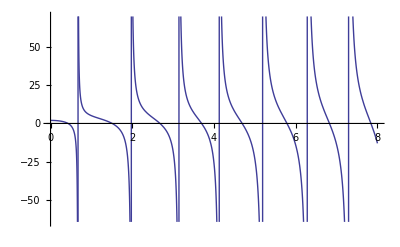

```mathematica
Plot[eq +2.0 /. {rA -> 3.0} ,{k,0.0, 8.0}, Ticks->{Automatic, Automatic}]
```

So, for each B < 0 we have extra state